# FindRandomTriangularGridMazeSolution

Find the solution to a random triangular grid maze

## Definition

## Definition

```mathematica
PositiveIntegerQ//ClearAll
```

```mathematica
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
PositiveIntegerQ::usage="PositiveIntegerQ[n] returns True when n is a strictly positive integer.";
```

```mathematica
ClearAll[VertexCoordinateList]
```

```mathematica
VertexCoordinateList[g_] := GraphEmbedding[g][[Last /@ Sort[Transpose[{VertexList[g], Range[VertexCount[g]]}]]]]
```

```mathematica
ClearAll[TriangularGridGraph]
```

```mathematica
TriangularGridGraph[{wide_Integer?Positive,high_Integer?Positive},opts:OptionsPattern[Graph]]:=Module[{cells,edges,vertices},cells=Flatten[Table[CirclePoints[{Sqrt[3] (2 j+k-2),3 k-2},{2,π/2},3],{j,wide},{k,high}],1];
edges=Union[Sort/@Flatten[Partition[#,2,1,1]&/@cells,1]];
vertices=Union[Flatten[edges,1]];
IndexGraph[Graph[UndirectedEdge@@@edges,opts,VertexCoordinates->Thread[vertices->vertices]]]]
```

```mathematica
ClearAll[GeneralizedTriangularGridGraph]
```

```mathematica
GeneralizedTriangularGridGraph[input:{m_?PositiveIntegerQ,n_?PositiveIntegerQ},opts:OptionsPattern[Graph]]:=Module[{vertexCoordinates,triangularGridGraph,vertices, vertexCoordinatesToVerticesAssociation,topPartDeletedGraph,subGraph,verticesToKeep},triangularGridGraph=TriangularGridGraph[input+1](*This line creates a triangular grid graph that is slightly larger than the desired size.*);

vertexCoordinates=VertexCoordinateList[triangularGridGraph](*This line gets the coordinates of each vertex in the graph.*);

vertices=VertexList[triangularGridGraph](*This line gets a list of all vertices in the graph.*);topPartDeletedGraph=VertexDelete[triangularGridGraph,Flatten[PositionLargest[vertexCoordinates,1,Order[Last[#1],Last[#2]]&]]](*-This line removes the top part of the graph.*);
vertexCoordinatesToVerticesAssociation=AssociationThread[vertexCoordinates->vertices](*This line creates an association that maps each vertex to its coordinates.*);verticesToKeep=Lookup[vertexCoordinatesToVerticesAssociation,Catenate[Values[Most/@SortBy[First]/@GroupBy[Last][vertexCoordinates]]]](*This line determines which vertices to keep in the final graph.*);
subGraph=Subgraph[topPartDeletedGraph,verticesToKeep,opts](*This line creates a subgraph of the original graph that contains only the vertices that were determined to be kept in the previous line.*)]
GeneralizedTriangularGridGraph::usage="GeneralizedTriangularGridGraph[{width, height}] generates a triangular grid graph with the specified width and height. The width and height should be positive integers.";
```

```mathematica
ClearAll[FindRandomTriangularGridMazeSolution]
```

```mathematica
FindRandomTriangularGridMazeSolution::usage="FindRandomTriangularGridMazeSolution[{StyleBox[\"m\", \"TI\"],StyleBox[\"n\", \"TI\"]}] finds a solution and other data for a random triangular grid maze of size StyleBox[\"m\", \"TI\"] by StyleBox[\"n\", \"TI\"].";
```

```mathematica
FindRandomTriangularGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges. This is known as the trivial graph, the singleton, or the unit graph.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)},opts:OptionsPattern[Graph]]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=GeneralizedTriangularGridGraph[{m1,n1},opts];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g],opts];maze=m;
start=1(*First@VertexList[m]*);end=Last@VertexList[m] (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"shortest-path-subgraph"->shortestPathSubgraph|>](*some ideas for other properties to add include deadends.*)
```

## Documentation

### Usage

FindRandomHexagonalTriangularMazeSolution[{m,n}]

finds a solution and other data for a random triangular grid maze of size m by n.

### Details & Options

There are three ways to tile the plane: with squares, which GridGraph does and the ResourceFunction FindRandomGridMazeSolution will make a maze for, with hexagons which the ResourceFunction HexagonalGridGraph does and FindRandomHexagonalGridMazeSolution will make a maze for, and with triangles which TriangularGridGraph does and the ResourceFunction FindRandomTriangularGridMazeSolution I am working on will make a maze for.

The shortest path data is iconized because the shortest-path might be very large. To get the data, use First on IconizedObject. You can also click the plus button and click Uniconize.

## Examples

### Basic Examples

Make a random 7 by 7 triangular grid maze:

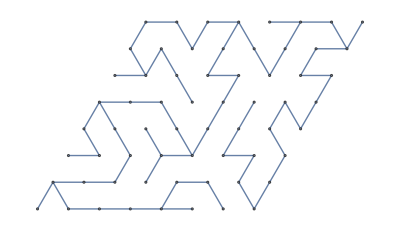
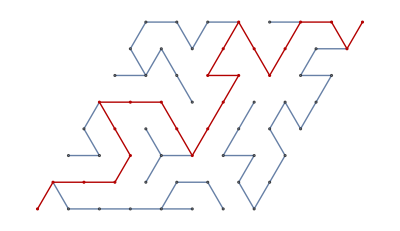
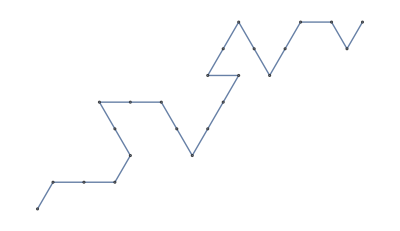
<|start→1,end→77,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→23,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{7,7}]
```

Make a random 10 by 10 triangular grid maze:

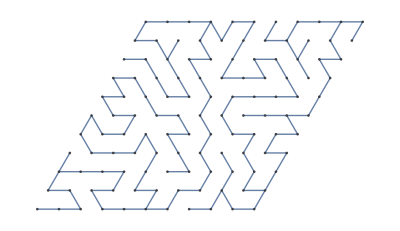
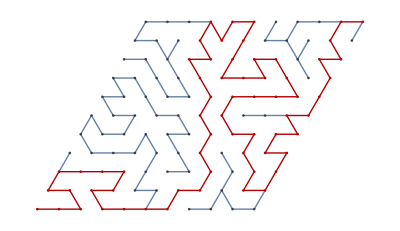
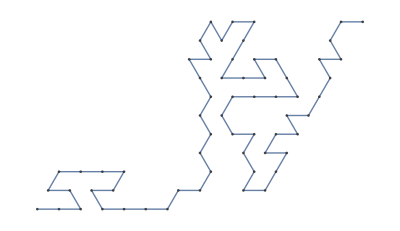
<|start→1,end→140,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→62,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{10,10}]
```

Make a random 15 by 15 triangular grid maze:

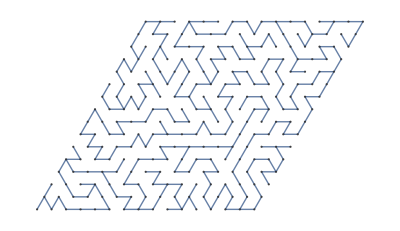
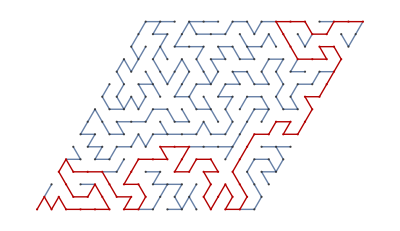
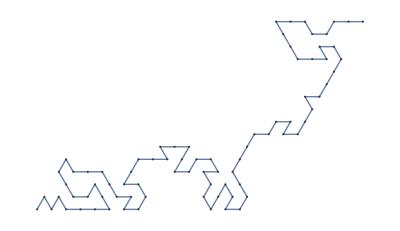
<|start→1,end→285,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→80,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{15,15}]
```

### Scope

Make a random rectangular 8 by 21 triangular grid maze:

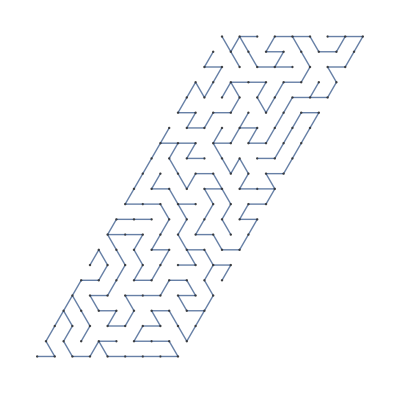
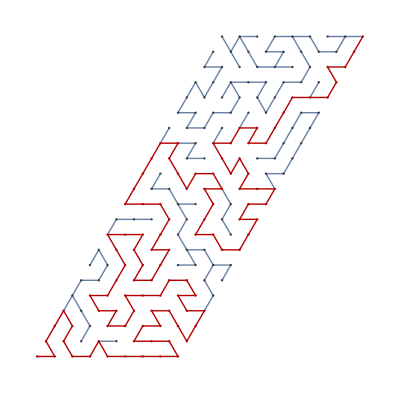
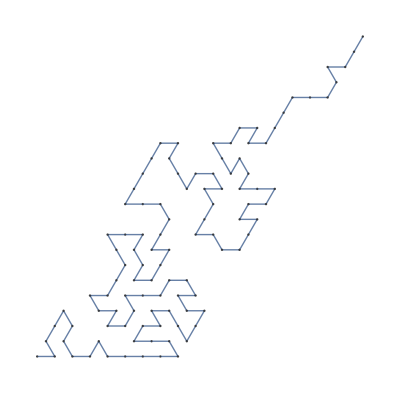
<|start→1,end→226,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→104,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{8,21}]
```

Make a random rectangular 21 by 8 triangular grid maze:

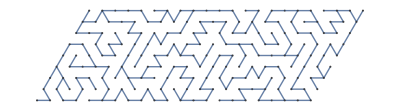
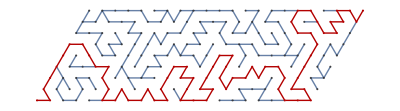
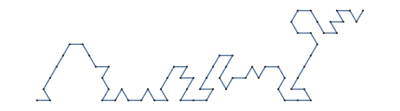
<|start→1,end→226,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→70,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{21,8}]
```

### Options

All graph options are supported. For example make the background of the graphs light blue:

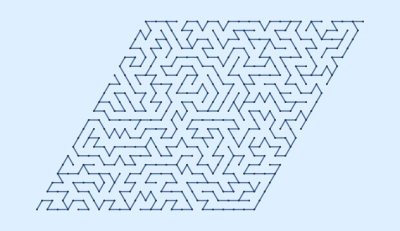
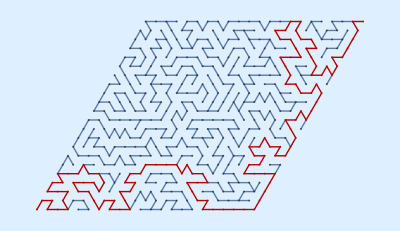
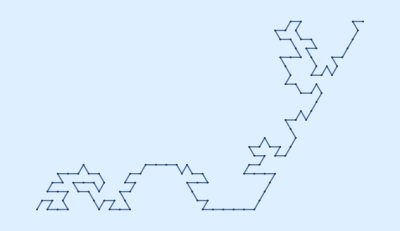
<|start→1,end→525,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→122,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{21,21},Background->LightBlue]
```

### Applications

Make a random 20 by 20 triangular grid maze:

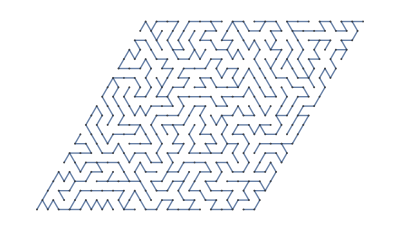
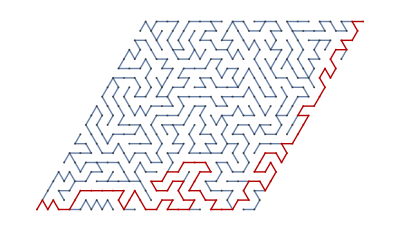
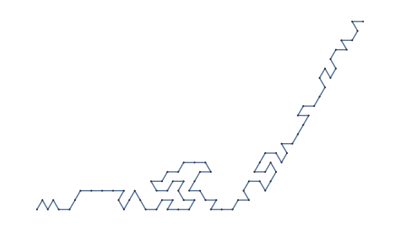
<|start→1,end→480,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→85,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{20,20}]
```

Make a random 25 by 25 triangular grid maze:

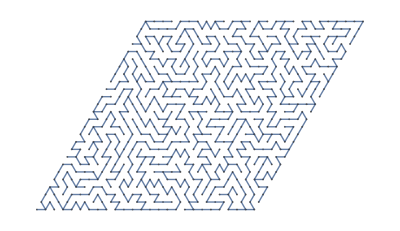
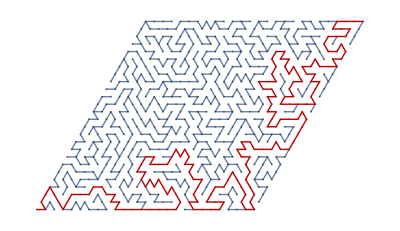
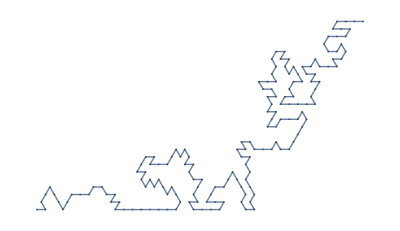
<|start→1,end→725,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→164,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{25,25}]
```

Make a random 30 by 30 triangular grid maze:

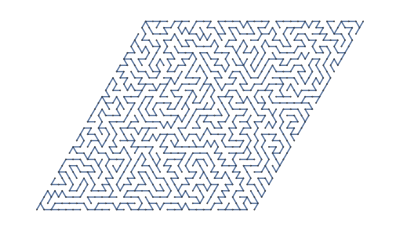
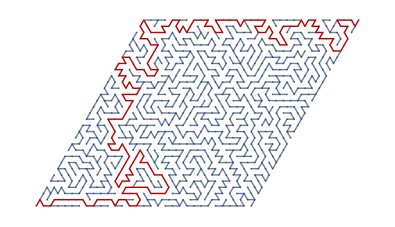
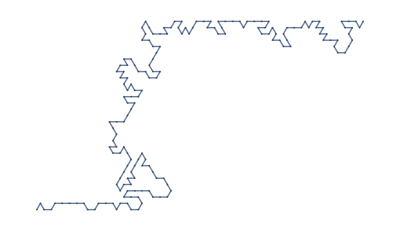
<|start→1,end→1020,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→169,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{30,30}]
```

Make a random 35 by 35 triangular grid maze:

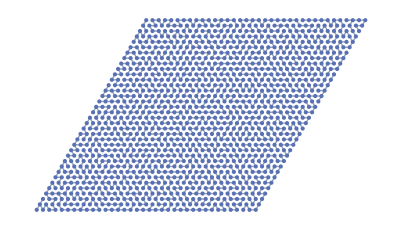
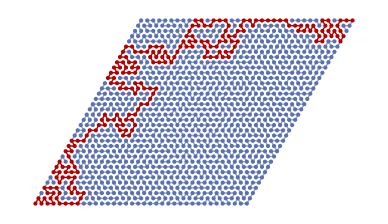
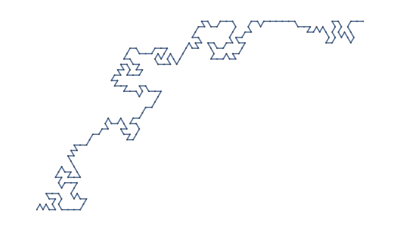
<|start→1,end→1365,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→212,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{35,35}]
```

Make a random 40 by 40 triangular grid maze:

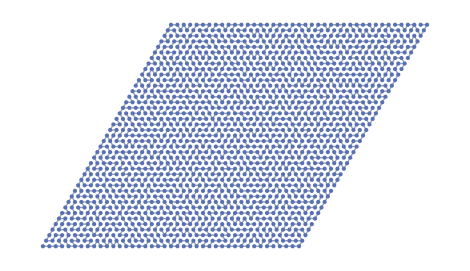
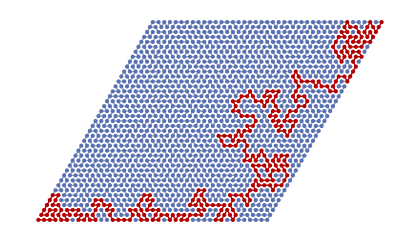
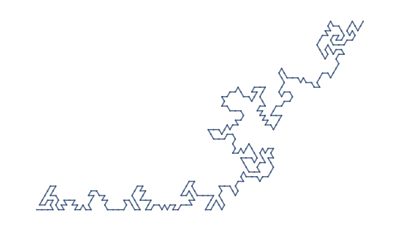
<|start→1,end→1760,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→297,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomTriangularGridMazeSolution[{40,40}]
```

Make a random 45 by 45 triangular grid maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{45,45}]]
```

1.12697

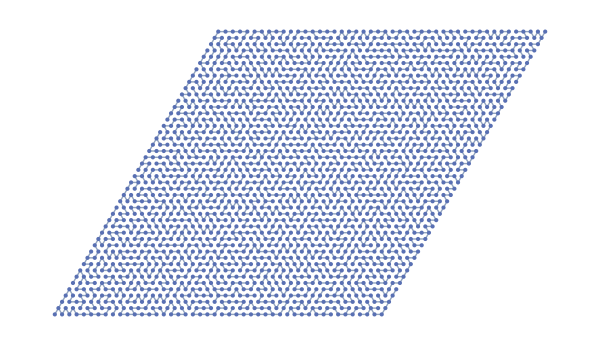
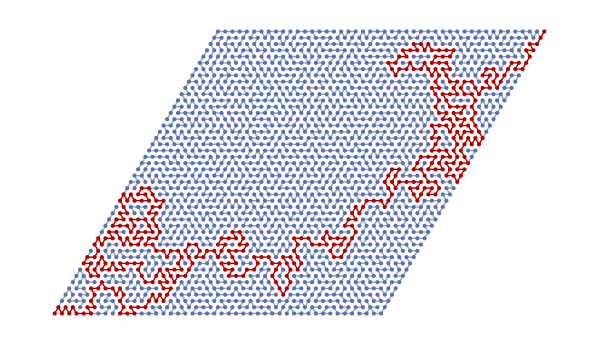
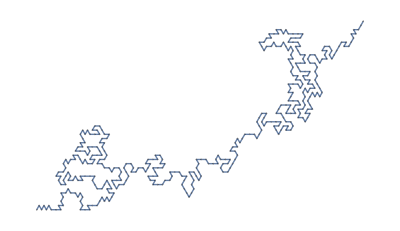
<|start→1,end→2205,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→408,shortest-path-subgraph→-Graphics-|>

Make a random 50 by 50 triangular grid maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{50,50}]]
```

1.50117

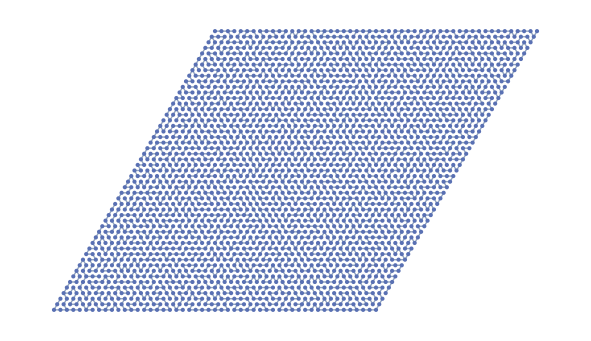
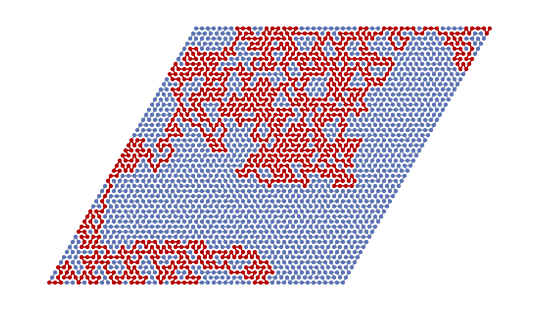
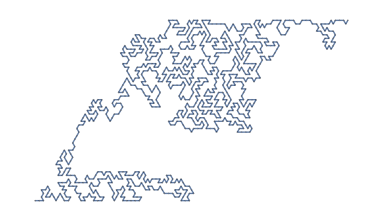
<|start→1,end→2700,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→965,shortest-path-subgraph→-Graphics-|>

Make a random 55 by 55 triangular grid maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{55,55}]]
```

2.09061

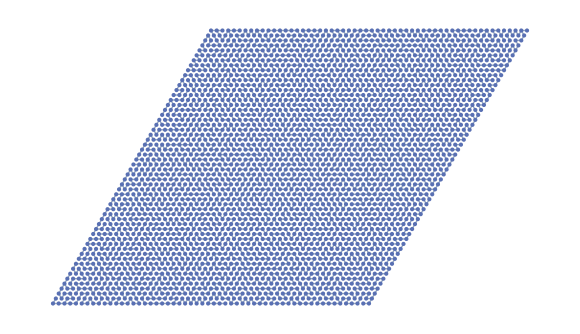
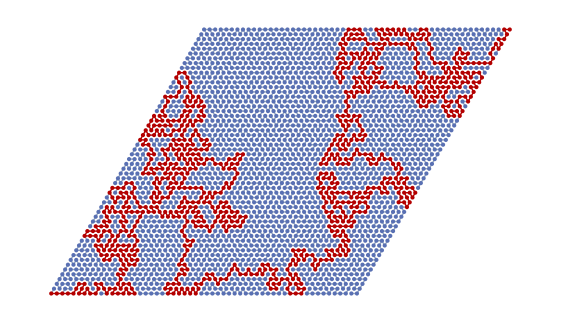
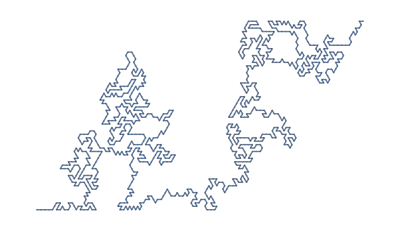
<|start→1,end→3245,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→919,shortest-path-subgraph→-Graphics-|>

Make a random 60 by 60 triangular grid maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{60,60}]]
```

2.69936

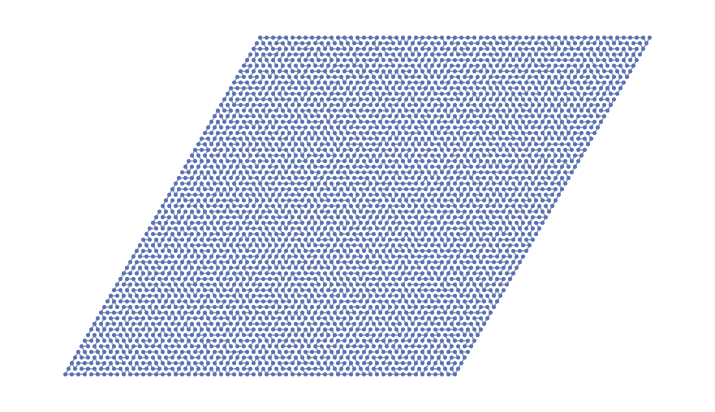
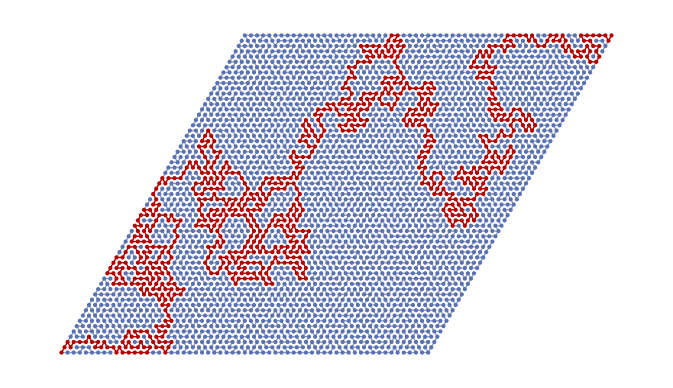
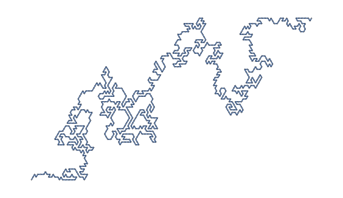
<|start→1,end→3840,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→826,shortest-path-subgraph→-Graphics-|>

Make a random 65 by 65 triangular grid maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{65,65}]]
```

3.54913

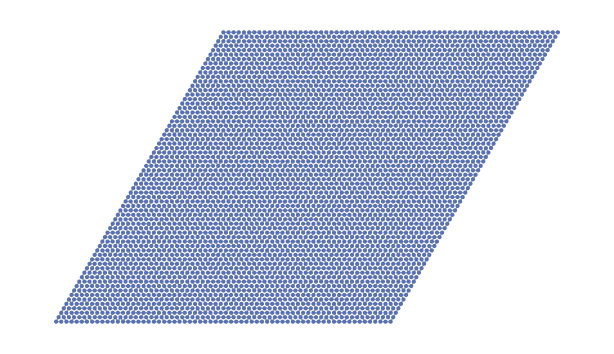
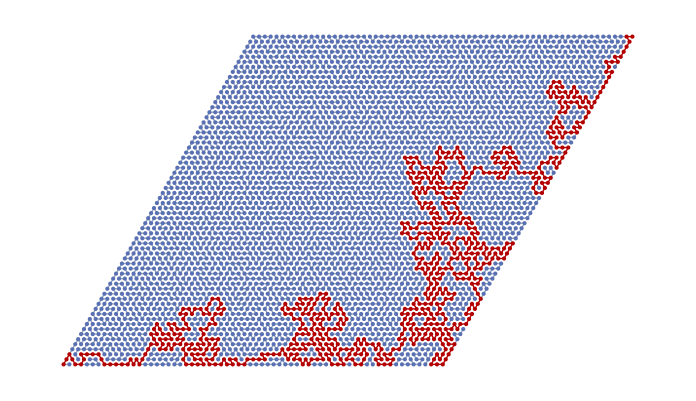
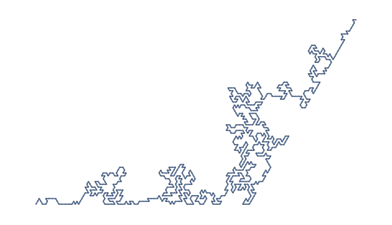
<|start→1,end→4485,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→725,shortest-path-subgraph→-Graphics-|>

Make a random 70 by 70 triangular grid maze.

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{70,70}]]
```

4.35297

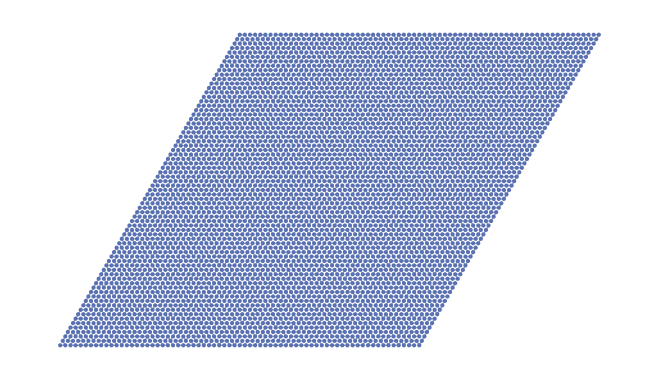
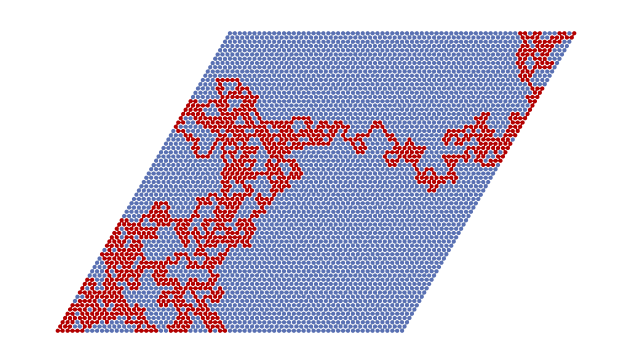
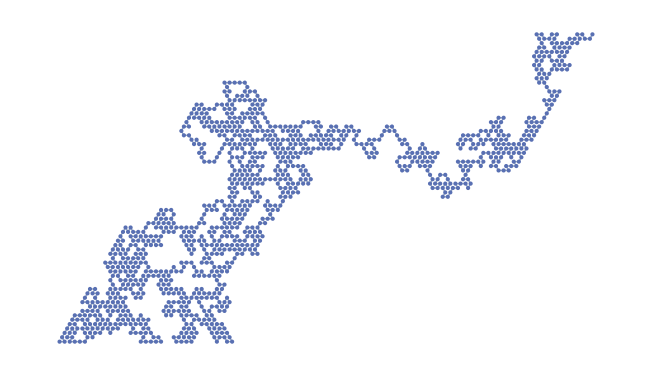
<|start→1,end→5180,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1178,shortest-path-subgraph→-Graphics-|>

Make a random 75 by 75 maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{75,75}]]
```

5.56006

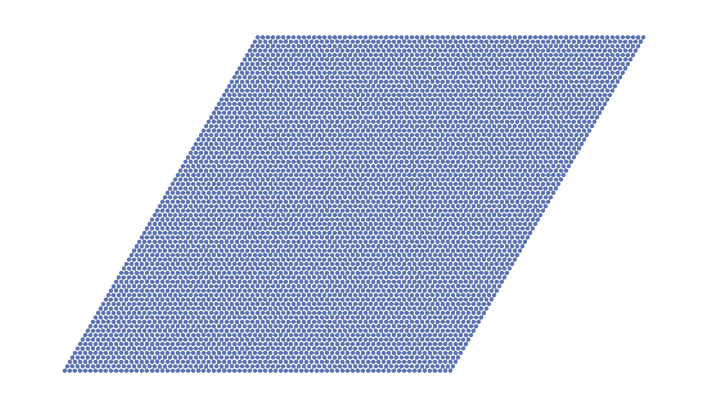
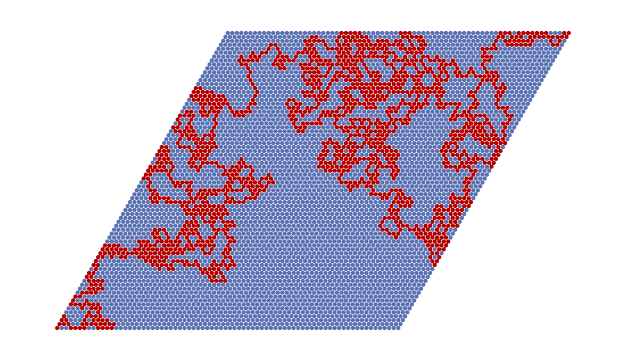
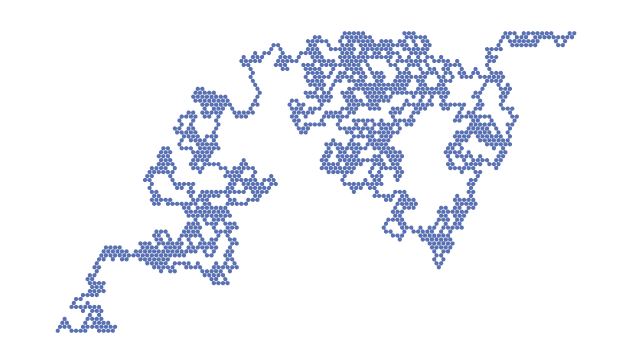
<|start→1,end→5925,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1625,shortest-path-subgraph→-Graphics-|>

Make a random 80 by 80 maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{80,80}]]
```

6.21669

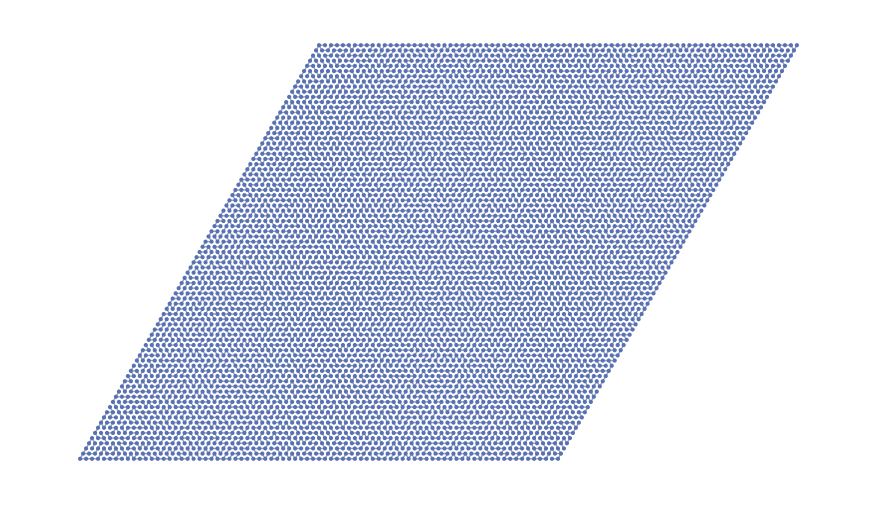
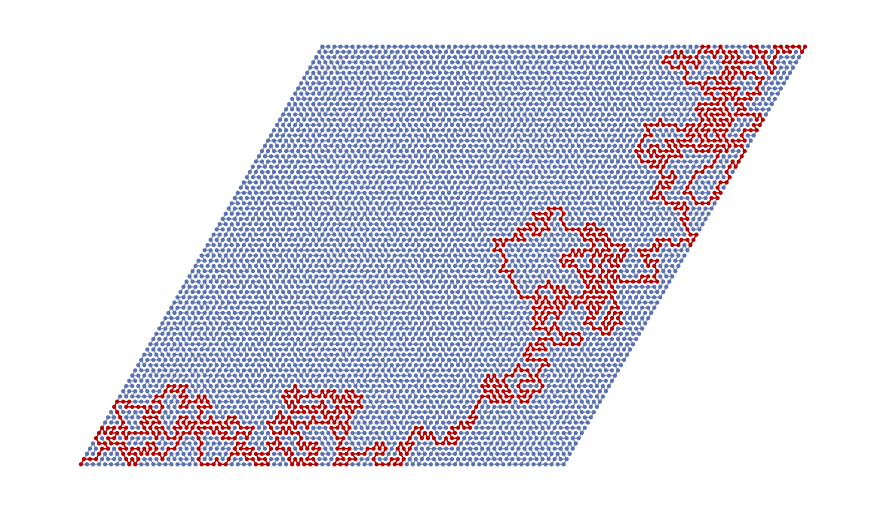
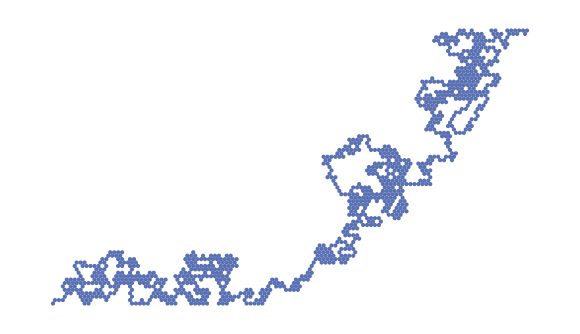
<|start→1,end→6720,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→1032,shortest-path-subgraph→-Graphics-|>

Make a random 95 by 95 maze:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{95,95}]]
```

14.5889

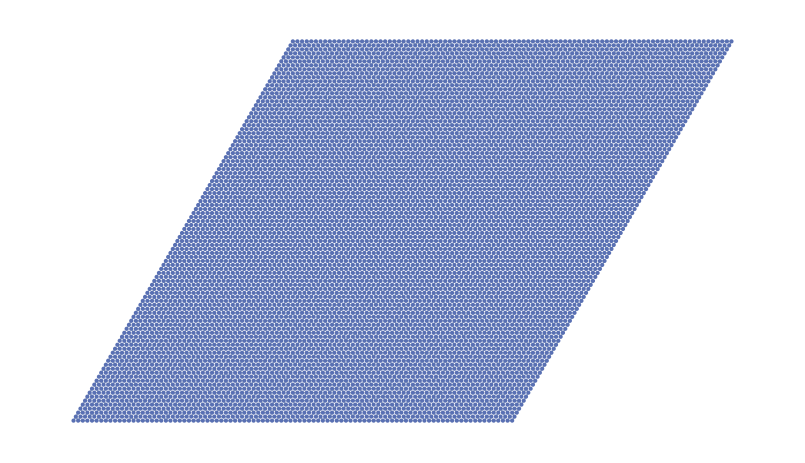
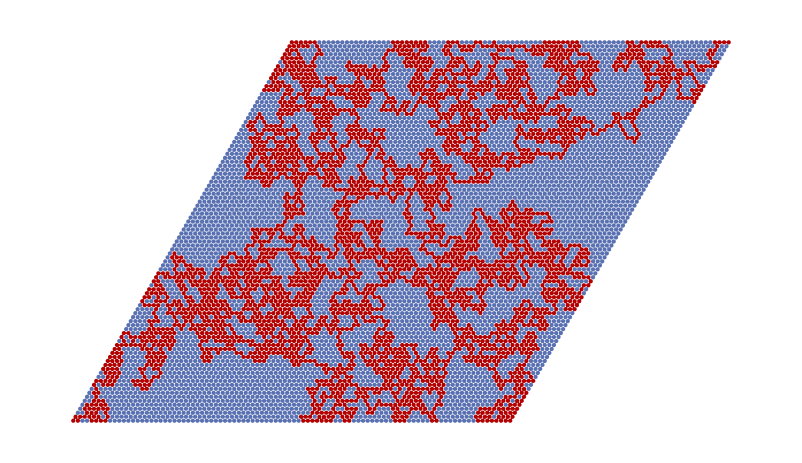
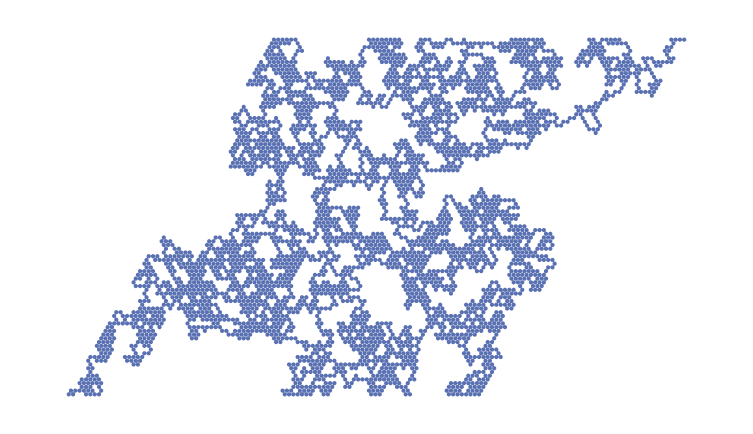
<|start→1,end→9405,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→3908,shortest-path-subgraph→-Graphics-|>

Larger inputs don't plot the maze and solved-maze graphs:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{100,100}]]
```

15.5559

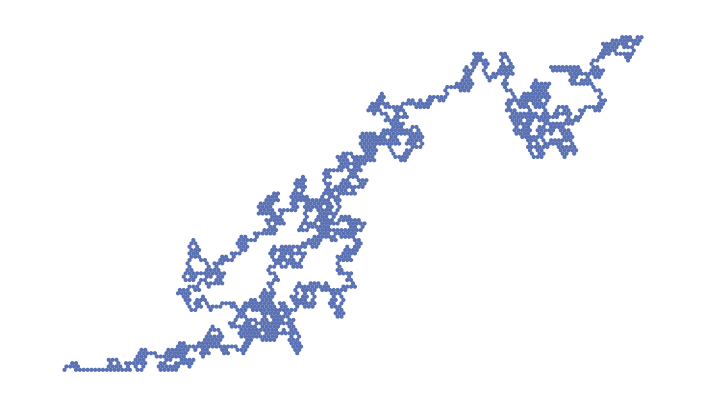
<|start→1,end→10400,maze→,solved-maze→,shortest-path→,distance→1495,shortest-path-subgraph→-Graphics-|>

Notice a visualization for maze and solved-maze is not available, but the shortest-path subgraph visualization is available.:

```mathematica
EchoTiming[FindRandomTriangularGridMazeSolution[{110,110}]]
```

18.9664

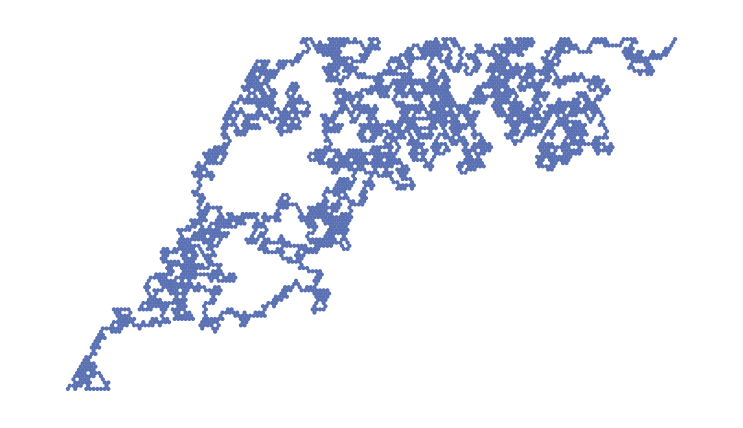
<|start→1,end→12540,maze→,solved-maze→,shortest-path→,distance→3045,shortest-path-subgraph→-Graphics-|>

Analyze the output graph to find the dead-ends with graph periphery:

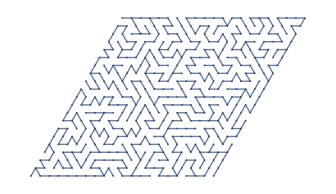

```mathematica
maze=FindRandomTriangularGridMazeSolution[{20,20}]["maze"]
```

{80,371}

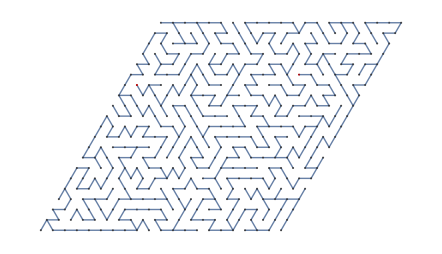

```mathematica
HighlightGraph[maze,Echo@GraphPeriphery[maze]]
```

### Properties and Relations

To get the data in Iconized Object, use First:

```mathematica
FindRandomTriangularGridMazeSolution[{10,10}]["shortest-path"]
```

```mathematica
FullForm[FindRandomTriangularGridMazeSolution[{10,10}]["shortest-path"]]
```

IconizedObject[List[1,3,5,8,9,16,12,20,30,25,21,26,31,43,49,61,67,55,62,68,74,80,92,99,105,93,81,75,69,57,52,58,64,76,70,82,89,84,96,108,101,106,113,123,128,135,140],"shortest-path",Rule[Method,Automatic]]

```mathematica
First[FindRandomTriangularGridMazeSolution[{10,10}]["shortest-path"]]
```

{1,3,2,5,4,8,7,10,11,13,9,16,20,25,31,36,42,49,54,66,73,85,90,97,103,110,104,92,80,75,69,64,76,88,81,87,99,105,100,112,122,117,106,101,89,96,108,113,123,119,128,135,140}

The data is iconized because the shortest-path might be very large. You can also click the plus button and click Uniconize:

-Graphics-

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Mazes

Graphs

Tiling of the plane

Triangles

Geometry

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.